```mathematica
ω=2 π 60.;
c = 3. 10^8;
```

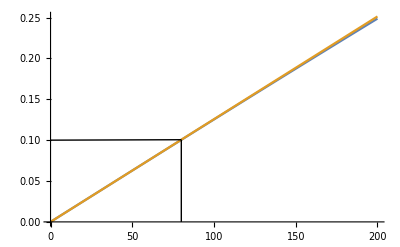

```mathematica
Plot[{Sin[ω/c x 10^3],ω/c x 10^3}, {x,0,200}, Epilog->{Line[{{80,0},{80,ω/c 80 10^3}}],Line[{{0,0.1},{80,ω/c 80 10^3}}]}, PlotRange->All]
```

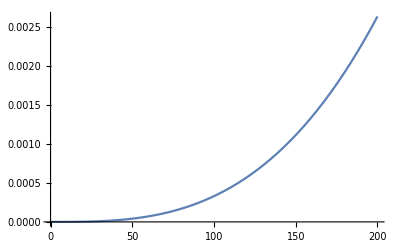

```mathematica
Plot[Abs[Sin[ω/c x 10^3]- ω/c x 10^3], {x,0,200}, PlotRange->All]
```

```mathematica
Sin[ω/c x 10^3]- ω/c x 10^3/.x-> 200
```

-0.00263753

```mathematica
Plot3D[Abs[Sin[k/c x 10^3]- k/c x 10^3], {x,0,200},{k,60,10 10^3}, PlotRange->All]
```

-Graphics3D-